# Program 1 Report

## Jonathan Pincince

## Program Setup

Getting to the program directory.

```mathematica
NBDirectory=ParentDirectory[NotebookDirectory[]];
ProgramDirectory=FileNameJoin[{NBDirectory,"csc450lib/SDK/Applications/Prog01"}];
SetDirectory[NotebookDirectory[]];
FileNames[];
```

## 1. Cosine Function

Here’s the first formula I decided to test. I created a file ‘cos.txt’ which stores the output of calling func() on my C++ implementation of the function, so I’ve read the file and created a sampling of points:

```mathematica
f[x_]:=Cos[0.01 x^2+1]/x
```

```mathematica
cosPoints=Import["cos.txt","Table"];
sampleCos=Table[cosPoints[[9*k]],{k,1,10}];
```

The following graph is just a line plot of points generated by my C++ implementation.

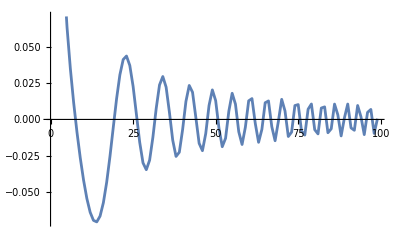

```mathematica
ListLinePlot[cosPoints]
```

Here is the graph of the actual function itself. These look quite similar, so I do believe the C++ program is getting respectably close values.

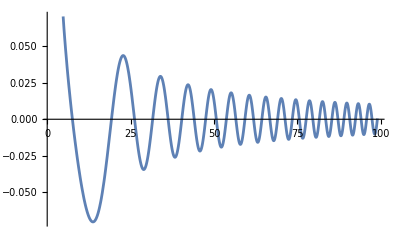

```mathematica
nbPlotPts=Dimensions[cosPoints][[1]];
xMin=cosPoints[[1]][[1]];
xMax=cosPoints[[nbPlotPts]][[1]];
plotF=Plot[f[x],{x,xMin,xMax}]
```

A few select points for comparison between the Mathematica results and the C++ results show that the C++ outputs are indeed quite close to Mathematica’s results:

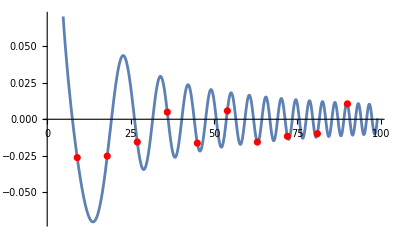

```mathematica
samplePlot=ListPlot[sampleCos,PlotStyle->Red];
Show[{plotF,samplePlot}]
```

Below is a comparison of the actual values produced. The first output box shows pairs of first a C++ produced value and then a Mathematica produced value. On first inspection these values are no different, but this is just because Mathematica will only show so many digits of any number without prompting. The next output box shows the actual difference between the values of each pair, and here we see the actual discrepancy between the C++ implementation and Mathematica’s results.

```mathematica
MMACosInputs=Table[cosPoints[[9*k]][[1]],{k,1,10}];
MMACosOutputs={};
For[k=1,k<=Dimensions[MMACosInputs][[1]],k++,
	MMACosOutputs=Append[MMACosOutputs,{MMACosInputs[[k]],N[f[MMACosInputs[[k]]]]}];
]
MMACosOutputs;

CosCVsMMA={};
For[k=1,k<=Dimensions[MMACosInputs][[1]],k++,
	CosCVsMMA=Append[CosCVsMMA,{cosPoints[[9*k]][[2]],N[f[MMACosInputs[[k]]]]}];
]

CosDiffs={};
For[k=1,k<=Dimensions[MMACosInputs][[1]],k++,
	CosDiffs=Append[CosDiffs,{CosCVsMMA[[k]][[1]]-CosCVsMMA[[k]][[2]]}];
]

CosRelativeErrs={};
For [k=1,k<=Dimensions[MMACosInputs][[1]],k++,
	CosRelativeErr=(100*(CosCVsMMA[[k]][[1]]-CosCVsMMA[[k]][[2]]))/CosCVsMMA[[k]][[2]];
	CosRelativeErrs=Append[CosRelativeErrs,{CosRelativeErr}];
]

CosCVsMMA
CosDiffs
CosRelativeErrs
```

{{-0.0263254,-0.0263254},{-0.0252786,-0.0252786},{-0.015642,-0.015642},{0.0048956,0.0048956},{-0.0163932,-0.0163932},{0.00573505,0.00573505},{-0.0156931,-0.0156931},{-0.0117149,-0.0117149},{-0.00992776,-0.00992776},{0.010552,0.010552}}

{{4.98539×10^-8},{7.23018×10^-9},{-1.08025×10^-8},{7.88544×10^-10},{-8.85618×10^-9},{6.24854×10^-10},{4.03027×10^-9},{4.07711×10^-8},{2.5143×10^-9},{2.55791×10^-8}}

{{-0.000189375},{-0.000028602},{0.0000690611},{0.0000161072},{0.0000540235},{0.0000108953},{-0.0000256818},{-0.000348027},{-0.000025326},{0.00024241}}

In the last output box I’ve calculated the relative rather than absolute errors of each discrepancy, all as percentages. In every case, the relative error is less than a percent of a percent.

## 2. Sine Function

The next formula, whose outputs I’ve saved in ‘sin.txt’. I’ve replicated most of the process with importing data and sampling points.

```mathematica
g[x_]:=Sin[0.005 x^2]/(E^x-E*x)
```

```mathematica
sinPoints=Import["sin.txt","Table"];
sampleSin=Table[sinPoints[[9*k]],{k,1,10}];
```

Again a line graph of the points generated by the C++ program.

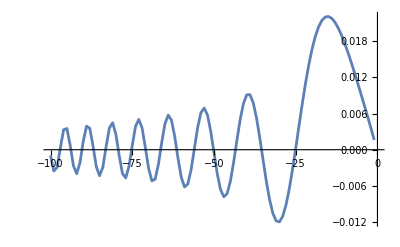

```mathematica
ListLinePlot[sinPoints]
```

Graph of g(x) as evaluated by MMA. Very similar looking graphs again.

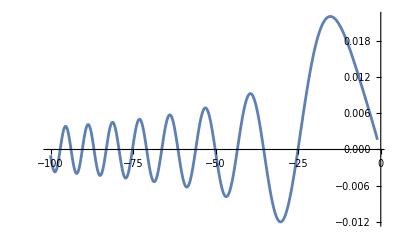

```mathematica
nbPlotPts=Dimensions[sinPoints][[1]];
xMin=sinPoints[[1]][[1]];
xMax=sinPoints[[nbPlotPts]][[1]];
plotG=Plot[g[x],{x,xMin,xMax}]
```

And again a graphical comparison of the C++ sample points on the MMA function graph.

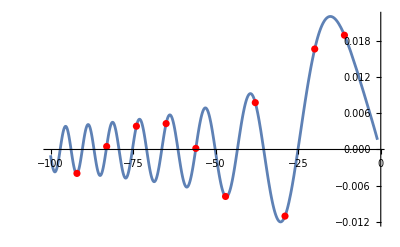

```mathematica
samplePlot=ListPlot[sampleSin,PlotStyle->Red];
Show[{plotG,samplePlot}]
```

Again here for consistency I’ve included a comparison of the actual values but just like with the cosine function, the values are the same up to the point that Mathematica will display. When the difference between the two values is found, again we see that the error is present but much smaller than the actual values produced, by several orders of magnitude.

```mathematica
MMASinInputs=Table[sinPoints[[9*k]][[1]],{k,1,10}];
MMASinOutputs={};
For[k=1,k<=Dimensions[MMASinInputs][[1]],k++,
	MMASinOutputs=Append[MMASinOutputs,{MMASinInputs[[k]],N[g[MMASinInputs[[k]]]]}];
]
MMASinOutputs;

SinCVsMMA={};
For[k=1,k<=Dimensions[MMASinInputs][[1]],k++,
	SinCVsMMA=Append[SinCVsMMA,{sinPoints[[9*k]][[2]],N[g[MMASinInputs[[k]]]]}];
]

SinDiffs={};
For[k=1,k<=Dimensions[MMASinInputs][[1]],k++,
	SinDiffs=Append[SinDiffs,{SinCVsMMA[[k]][[1]]-SinCVsMMA[[k]][[2]]}]
]

SinRelativeErrs={};
For [k=1,k<=Dimensions[MMACosInputs][[1]],k++,
	SinRelativeErr=(100*(CosCVsMMA[[k]][[1]]-CosCVsMMA[[k]][[2]]))/CosCVsMMA[[k]][[2]];
	SinRelativeErrs=Append[SinRelativeErrs,{SinRelativeErr}];
]

SinCVsMMA
SinDiffs
SinRelativeErrs
```

{{-0.00398196,-0.00398196},{0.000497665,0.000497665},{0.00387662,0.00387662},{0.00431177,0.00431177},{0.000183674,0.000183674},{-0.00781766,-0.00781766},{0.00779977,0.00779977},{-0.0110873,-0.0110873},{0.0167256,0.0167256},{0.0190214,0.0190214}}

{{1.93801×10^-9},{-1.52147×10^-10},{4.68788×10^-9},{-2.15508×10^-9},{-4.78227×10^-10},{3.53411×10^-9},{-3.6262×10^-9},{3.03722×10^-8},{8.53867×10^-9},{-3.25365×10^-8}}

{{-0.000189375},{-0.000028602},{0.0000690611},{0.0000161072},{0.0000540235},{0.0000108953},{-0.0000256818},{-0.000348027},{-0.000025326},{0.00024241}}

The last output shows the percent relative errors of all the measurements. These are again all less than a percent of a percent; so far it looks as though C++ isn’t doing too bad.

## 3. Polynomial 1

The first instance of a 1D polynomial looked like this:

```mathematica
h[x_]:=1 x^4-2 x^3+3 x^2-4 x^1+5 x^0
```

```mathematica
p1Points=Import["p1.txt","Table"];
sampleP1=Table[p1Points[[9*k]],{k,1,9}];
```

Graph of points from C++ code:

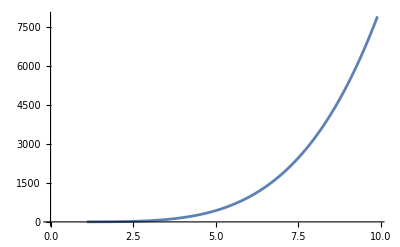

```mathematica
ListLinePlot[p1Points]
```

Graph of MMA function. This looks basically the same as the C++ graph, but again we’ll look at some numbers.

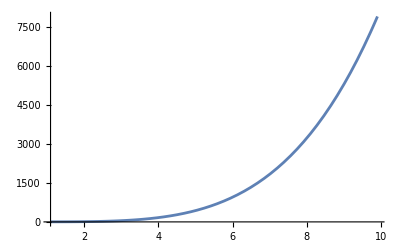

```mathematica
nbPlotPts=Dimensions[p1Points][[1]];
xMin=p1Points[[1]][[1]];
xMax=p1Points[[nbPlotPts]][[1]];
plotP1=Plot[h[x],{x,xMin,xMax}]
```

A selection of points from C++ code to compare to MMA function graph:

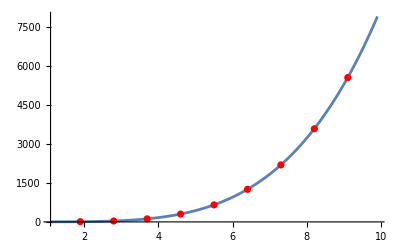

```mathematica
samplePlot=ListPlot[sampleP1,PlotStyle->Red];
Show[{plotP1,samplePlot}]
```

The same comparison of values as with the sine and cosine function, with C++ values first and Mathematica values second, within the pairs. For once there is actually a visible difference between the values themselves, but only because we’re working with much larger numbers because of the nature of the polynomial. The absolute errors are a bit larger now, but

```mathematica
MMAP1Inputs=Table[p1Points[[9*k]][[1]],{k,1,9}];
MMAP1Outputs={};
For[k=1,k<=Dimensions[MMAP1Inputs][[1]],k++,
	MMAP1Outputs=Append[MMAP1Outputs,{MMAP1Inputs[[k]],N[h[MMAP1Inputs[[k]]]]}];
]

MMAP1Outputs;
P1CVsMMA={};
For[k=1,k<=Dimensions[MMAP1Inputs][[1]],k++,
	P1CVsMMA=Append[P1CVsMMA,{p1Points[[9*k]][[2]],N[h[MMAP1Inputs[[k]]]]}];
]

P1Diffs={};
For[k=1,k<=Dimensions[MMAP1Inputs][[1]],k++,
	P1Diffs=Append[P1Diffs,{P1CVsMMA[[k]][[1]]-P1CVsMMA[[k]][[2]]}];
]

P1RelativeErrs={};
For [k=1,k<=Dimensions[MMAP1Inputs][[1]],k++,
	P1RelativeErr=(100*(P1CVsMMA[[k]][[1]]-P1CVsMMA[[k]][[2]]))/P1CVsMMA[[k]][[2]];
	P1RelativeErrs=Append[P1RelativeErrs,{P1RelativeErr}];
]

P1CVsMMA
P1Diffs
P1RelativeErrs
```

{{7.5441,7.5441},{34.8816,34.8816},{117.38,117.38},{303.153,303.154},{656.061,656.063},{1255.71,1255.71},{2197.45,2197.46},{3592.39,3592.4},{5567.38,5567.38}}

{{-1.77636×10^-15},{7.10543×10^-15},{-0.0001},{-0.0006},{-0.0015},{-0.0036},{-0.0101},{-0.0116},{-0.0041}}

{{-2.35463×10^-14},{2.03701×10^-14},{-0.0000851933},{-0.000197919},{-0.000228637},{-0.00028669},{-0.000459622},{-0.000322904},{-0.0000736432}}

The relative errors remain quite small. However, as the inputs grow, the errors also grow, whereas before the relative errors appeared to remain within a certain range because of the wave-nature of the functions.

## 4. Polynomial 2

1D polynomial 2:

```mathematica
l[x_]:=5 x^4-4 x^3+3 x^2-2 x^1+1 x^0
```

```mathematica
p2Points=Import["p2.txt","Table"];
sampleP2=Table[p2Points[[9*k]],{k,1,9}];
```

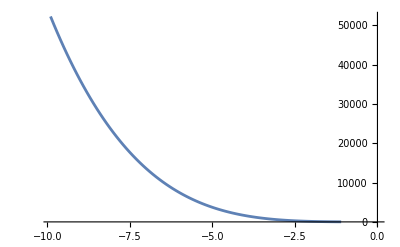

```mathematica
ListLinePlot[p2Points]
```

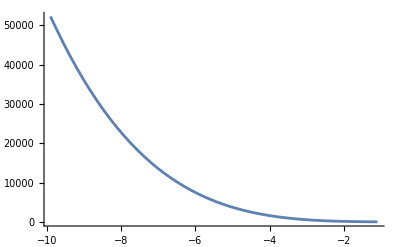

```mathematica
nbPlotPts=Dimensions[p2Points][[1]];
xMin=p2Points[[1]][[1]];
xMax=p2Points[[nbPlotPts]][[1]];
plotP2=Plot[l[x],{x,xMin,xMax}]
```

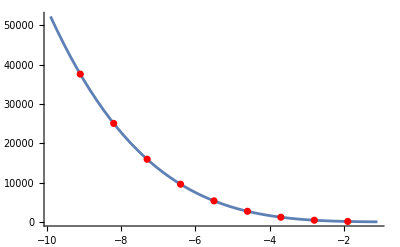

```mathematica
samplePlot=ListPlot[sampleP2,PlotStyle->Red];
Show[{plotP2,samplePlot}]
```

```mathematica
MMAP2Inputs=Table[p2Points[[9*k]][[1]],{k,1,9}];
MMAP2Outputs={};
For[k=1,k<=Dimensions[MMAP2Inputs][[1]],k++,
	MMAP2Outputs=Append[MMAP2Outputs,{MMAP2Inputs[[k]],N[l[MMAP2Inputs[[k]]]]}];
]
MMAP2Outputs;

P2CVsMMA={};
For[k=1,k<=Dimensions[MMAP2Inputs][[1]],k++,
	P2CVsMMA=Append[P2CVsMMA,{p2Points[[9*k]][[2]],N[l[MMAP2Inputs[[k]]]]}];
]

P2Diffs={};
For[k=1,k<=Dimensions[MMAP2Inputs][[1]],k++,
	P2Diffs=Append[P2Diffs,{P2CVsMMA[[k]][[1]]-P2CVsMMA[[k]][[2]]}];
]

P2RelativeErrs={};
For [k=1,k<=Dimensions[MMAP2Inputs][[1]],k++,
	P2RelativeErr=(100*(P2CVsMMA[[k]][[1]]-P2CVsMMA[[k]][[2]]))/P2CVsMMA[[k]][[2]];
	P2RelativeErrs=Append[P2RelativeErrs,{P2RelativeErr}];
]

P2CVsMMA
P2Diffs
P2RelativeErrs
```

{{37569.3,37569.4},{25030.6,25030.6},{15930.6,15930.6},{9573.83,9573.81},{5343.54,5343.56},{2701.74,2701.75},{1189.16,1189.16},{425.255,425.256},{108.226,108.226}}

{{-0.0945},{0.0388542},{0.026156},{0.0237479},{-0.0225},{-0.012},{-0.0025},{-0.001},{-0.0005}}

{{-0.000251535},{0.000155227},{0.000164188},{0.00024805},{-0.000421067},{-0.000444156},{-0.000210232},{-0.000235152},{-0.000461994}}

Absolute and relative error which remain low. Overall it appears that the C++ implementation held up well, but in the case of the polynomial functions I didn’t test using terribly complex or large polynomials, for the sake of making testing straightforward in the C++ program itself.